# Guppy video analysis

These functions are for analyzing videos taken using the guppy/infinity camera. Functions are found in functions_guppy.wl
Last updated 06/01/16 by Leanne Friedrich
This notebook has only been tested in Mathematica 10. 
Note: This notebook imports .avi videos. For reasons I cannot explain, Mathematica uses Quicktime to parse videos, so Quicktime MUST BE INSTALLED on your computer, otherwise you will get errors out the wazoo.

## Initialization

establish a working directory as the directory that this file is in
import needed functions
this step will create a variable “video” which will be a list of all of the guppy videos with CSph particles in any child directory of your working directory

```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions_guppy.wl;
```

```mathematica
Length[video]
```

632

you can also create your own custom list of guppy files using this format
“guppy*avi” is a generic name for any file that starts with guppy and ends with avi
{“LF66”} means that you’re only going to search in the subdirectories LF66 and LF59. “*” would mean search in all folders.
Infinity means that you will search for files in all of the subfolders and subsubfolders of the folders you chose. If you only want files directly in this folder, this should be 1, etc.

```mathematica
v2 = FileNames["guppy*avi", {"LF66", "LF59"}, Infinity];
```

columnIndex is a handy function in functions_master.wl that helps you visualize lists (this is a simple function; you should just run it to see what it does)

```mathematica
Grid[columnIndex[v2]]
```

You can also use FileNames to get folders instead.

```mathematica
dirs = Select[FileNames["*CSph*P*", "LF66", Infinity], DirectoryQ[#]&];
Length[dirs]
```

73

## Analysis

master_functions creates a variable called directories, which consists of all sample - specific folders in this working directory

```mathematica
Length[directories]
```

634

```mathematica
Do[Print[i]; Print[getGuppy[directories[[i]]]], {i,551,634}]
```

Analyzing videos

To analyze a guppy video, use analyzeAndExport
The input variables should be
[video file name, background subtraction parameter (this isn’t used in this version), fraction through the video to start taking measurements, fraction through the video to stop taking measurements, minimum slope of the left channel edge, maximum slope of the left channel edge, and edge detection parameter (usually around 0.1)]
“slope” in this case means the # of pixels between the horizontal position of the top and bottom of the channel’s left edge

This will export 6 files into the same folder that the video is in.
 - the location of the channel
 - the composite profile superimposed on a frame cropped to the channel width
 - stats about the video
 - the composite intensity profile
 - stats for each line profile
 - all captured line profiles

When you run analyzeAndExport, you should print out the results as I do below. Use the output to detect any problems with the algorithm. If there is a problem, it will probably be a line detection problem. In that case, you should go to the troubleshooting section.

1

LF59\SiO6.5_A16_CSph120\V0\LF59_SiO6.5_A16_CSph120_V0_P1404_S5_t16_04_08_17_05_07\guppy_LF59_SiO6.5_A16_CSph120_V0_P1404_S5_t16_04_08_17_05_07.avi

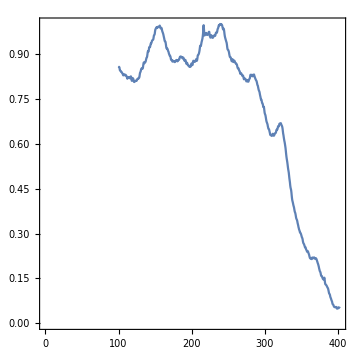
-Graphics-Mean center | Mean STDEV
221.93 | 72.2535
STDEV center | STDEV STDEV
4.76212 | 2.69895
Composite Center | Composite STDEV
222.065 | 72.3926-Graphics-

```mathematica
v65 = FileNames["*guppy*6.5*avi*", "*", Infinity];
Do[Print[i];Print@analyzeAndExport[v65[[i]],  0.25, 0.75, -20, 120, 0.1]; , {i,1, 1}];
```

As you’re fixing problems, it can be helpful to use parseGuppyName to automatically get sample info out of a guppy file name

```mathematica
problems = v65[[{1,5,10}]];
```

```mathematica
Length@problems
```

23

```mathematica
Grid[Prepend[parseGuppyName/@problems, {"Notebook page", "Silica wt%", "Acetone wt%", "Particle wt", "Voltage", "Pressure", "Speed", "Time"}]]
```

Notebook page | Silica wt% | Acetone wt% | Particle wt | Voltage | Pressure | Speed | Time
59 | 6.5 | 16 | 120 | 0 | 1404 | 5 | 16_04_08_17_05_07
59 | 6.5 | 16 | 120 | 0 | 2837 | 20 | 16_04_08_17_07_20
59 | 6.5 | 16 | 120 | 15 | 1404 | 5 | 16_04_08_16_56_19

Troubleshooting

When the algorithm fails, it’s usually because it couldn’t find the channel. To fix this, play around with the parameters you use to get the line using getLine. If none of this works, you will need to modify the getLine code.

input should be [guppy file, True (if true, it will print out information that will help you diagnose the problem), fraction through the video to take your calibration frame from (e.g. 0.25), min slope, max slope, straight edge detection parameter]

the function will print out an edge detected image, where it will only consider white points. Then, it will print out your original frame, but it will draw potential left edges on the picture in orange. The function will take the leftmost line as the left edge of the channel.

If the channel is slanted too far from vertical, you may need to change the min and max slope. However, it’s best not to leave a big range for those slopes, because sometimes the algorithm will detect the sides of the chip if you are too lenient with the slope.

If that doesn’t work, you should play with different values for the straight edge parameter. Usually, this value will be around 0.1, but sometimes it can go all the way up to 0.8. 

If you end up with a funny-looking intensity profile, it may be because the channel moved during the video, or a clog happens. If that’s true, then go back to analyzeAndExport and modify your start and finish times.

When you get the algorithm to correctly identify the channel edge, write down what parameters you used for that file! AnalyzeAndExport will NOT record this information, so you need to keep track of it yourself, in case you need to go back and redo things.

```mathematica
getLine[v65[[1]], True, 0.25,  -20, 120, 0.1];
```

0.996909

-Graphics-

-Graphics-